=== RÉSULTATS DU FIT ===

General::munfl: Exp[-4550.55] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
AhFit | 1.00927 | 0.000682809 | 1478.11 | 0.

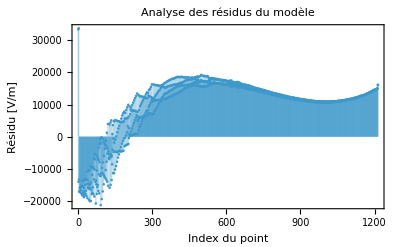

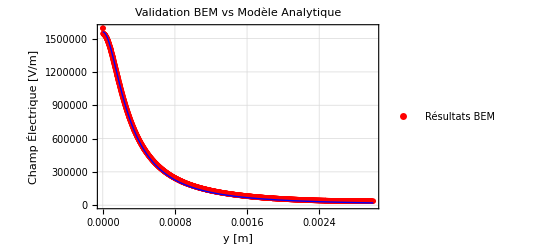

```mathematica
(* =======================================================================*)(*ANALYSE DU CHAMP ÉLECTRIQUE-ÉTUDE DE VALIDATION BEM vs ANALYTIQUE*)(* =======================================================================*)(*-----------------------------------------------------------------------*)(*SECTION 0-CONFIGURATION& CONSTANTES*)(*-----------------------------------------------------------------------*)(*Chemin du fichier de validation BEM*)
(*fileValidation="/Users/Kevin/BEMinterface/BEM/dataMathematica/Electric Field.msh_LevelsetSimpleTest.txt";*)

(*Constantes physiques et géométriques (SI)*)
(*scale=1*^-6;
gVal=100*scale;            (*Gap g=100 um*)
wVal=200*scale;            (*Largeur w=200 um*)
v0Val=2000.0;               (*Delta V=2000 V*)*)
fileValidation="/Users/Kevin/BEMinterface/BEM/dataMathematica/microtas_BEM_analytical_match";

scale=1*^-6;
gVal=400*scale;            (*Gap g=100 um*)
wVal=400*scale;            (*Largeur w=200 um*)
v0Val=1000.0;               (*Delta V=2000 V*)

a=gVal/2;                (*50 um*)
b=gVal/2+wVal;         (*250 um*)
kMod=gVal/(gVal+2*wVal);
Kk=EllipticK[kMod^2];

(*-----------------------------------------------------------------------*)
(*SECTION 1-FONCTIONS UTILITAIRES DE TRAITEMENT*)
(*-----------------------------------------------------------------------*)

(*Importation et extraction des points uniques {x,y, |E|}*)
ImportAndExtractPoints[file_String]:=Module[{rawData,pts1,pts2},rawData=Import[file,"Table"];
pts1=rawData[[All,{1,6,8}]];
pts2=rawData[[All,{11,16,18}]];
DeleteDuplicates[Join[pts1,pts2]]];

(*Tri le long de l'axe y et extraction des paires {y, |E|}*)
GetYProfile[file_String]:=Module[{pts,sortedPts},pts=ImportAndExtractPoints[file];
sortedPts=SortBy[pts,#[[2]]&];
Transpose[{sortedPts[[All,2]],sortedPts[[All,3]]}]];

(*-----------------------------------------------------------------------*)
(*SECTION 2-MODÈLE ANALYTIQUE& FITTING*)
(*-----------------------------------------------------------------------*)

(*Modèle analytique (champ E(y) entre électrodes coplanaires)*)
modelEx[y_,AhFit_]:=(AhFit*v0Val/(2*Kk*a))/Sqrt[(1+(y/a)^2)*(1+(y/b)^2)];

(*Chargement des données BEM*)
dataBEM=GetYProfile[fileValidation];

(*Ajustement non-linéaire du facteur AhFit*)
fitResult=NonlinearModelFit[dataBEM,modelEx[y,AhFit],{{AhFit,1.0}},y];
ahEstimated=AhFit/. fitResult["BestFitParameters"];

(*Affichage du tableau de paramètres et de l'analyse des résidus*)
Print["=== RÉSULTATS DU FIT ==="];
Print[fitResult["ParameterTable"]];

ListPlot[fitResult["FitResiduals"],Filling->Axis,Frame->True,FrameLabel->{"Index du point","Résidu [V/m]"},PlotLabel->"Analyse des résidus du modèle"]

(*-----------------------------------------------------------------------*)
(*SECTION 3-VISUALISATION ET COMPARAISON*)
(*-----------------------------------------------------------------------*)

yMax=Max[dataBEM[[All,1]]];
eMax=Max[dataBEM[[All,2]]];

Show[ListPlot[dataBEM,PlotStyle->Directive[Red,AbsolutePointSize[4]],PlotLegends->{"Résultats BEM"}],Plot[fitResult[y],{y,0,yMax},PlotStyle->Directive[Thick,Blue],PlotRange->{{0,yMax},{0,eMax*1.1}}],Frame->True,FrameLabel->{"y [m]","Champ Électrique [V/m]"},GridLines->Automatic,PlotLabel->"Validation BEM vs Modèle Analytique",PlotLegends->LineLegend[{Red,Blue},{"Résultats BEM",Row[{"Analytique (A_h = ",NumberForm[ahEstimated,{4,3}],")"}]}]]
```

=== RÉSULTATS DU FIT (zone y > 200 um) ===

General::munfl: Exp[-2850.7] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
AhFit | 1.1738 | 0.00224879 | 521.97 | 0.

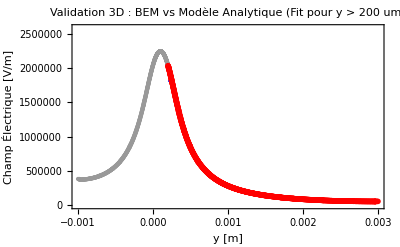

```mathematica
(* =======================================================================*)(*ANALYSE DU CHAMP ÉLECTRIQUE-ÉTUDE DE VALIDATION (ÉLECTRODES ÉPAISSES)*)(* =======================================================================*)(*-----------------------------------------------------------------------*)(*SECTION 0-CONFIGURATION& CONSTANTES*)(*-----------------------------------------------------------------------*)fileValidation="/Users/Kevin/BEMinterface/BEM/dataMathematica/microtas_BEM_analytical_match_thick_electrodes.txt";

(*Constantes géométriques (du.geo)*)
scale=1*^-6;
gVal=400*scale;           (*Gap g=400 um*)
wVal=400*scale;           (*Largeur w=400 um*)
hElec=200*scale;           (*Haut des électrodes y=200 um*)
v0Val=1000.0;              (*Delta V=1000 V*)

a=gVal/2;               (*200 um*)
b=gVal/2+wVal;        (*600 um*)
kMod=gVal/(gVal+2*wVal);
Kk=EllipticK[kMod^2];

(*-----------------------------------------------------------------------*)
(*SECTION 1-FONCTIONS UTILITAIRES DE TRAITEMENT*)
(*-----------------------------------------------------------------------*)

ImportAndExtractPoints[file_String]:=Module[{rawData,pts1,pts2},rawData=Import[file,"Table"];
pts1=rawData[[All,{1,6,8}]];
pts2=rawData[[All,{11,16,18}]];
DeleteDuplicates[Join[pts1,pts2]]];

GetYProfile[file_String]:=Module[{pts,sortedPts},pts=ImportAndExtractPoints[file];
sortedPts=SortBy[pts,#[[2]]&];
Transpose[{sortedPts[[All,2]],sortedPts[[All,3]]}]];

(*-----------------------------------------------------------------------*)
(*SECTION 2-TRAITEMENT ET FIT (SEULEMENT POUR y>hElec)*)
(*-----------------------------------------------------------------------*)

If[!FileExistsQ[fileValidation],Print["⚠️ ERREUR : Fichier non trouvé : ",fileValidation];
Abort[];];

dataBEMAll=GetYProfile[fileValidation];

(*FILTRAGE STRICT*)
dataBEM=Select[dataBEMAll,#[[1]]>hElec&];
dataBEMBelow=Select[dataBEMAll,#[[1]]<=hElec&];

(*Modèle analytique translaté (origine relative à y=hElec)*)
modelEx[y_,AhFit_]:=(AhFit*v0Val/(2*Kk*a))/Sqrt[(1+((y-hElec)/a)^2)*(1+((y-hElec)/b)^2)];

(*Fitting uniquement sur la zone y>hElec (avec Quiet pour éviter les sous-flux numériques)*)
Quiet[fitResult=NonlinearModelFit[dataBEM,modelEx[y,AhFit],{{AhFit,1.0}},y],{General::underflow,General::munfl}];

ahEstimated=AhFit/. fitResult["BestFitParameters"];

Print["=== RÉSULTATS DU FIT (zone y > ",hElec/scale," um) ==="];
Print[fitResult["ParameterTable"]];

(*-----------------------------------------------------------------------*)
(*SECTION 3-VISUALISATION DU PROFILE COMPLET*)
(*-----------------------------------------------------------------------*)

yMin=Min[dataBEMAll[[All,1]]];
yMax=Max[dataBEMAll[[All,1]]];
eMax=Max[dataBEMAll[[All,2]]];

Show[(*1. LE PLOT DU MODÈLE EN PREMIER:définit la grille continue et empêche le rognage à hElec*)Plot[fitResult[y],{y,hElec,yMax},PlotStyle->Directive[Thick,Blue],PlotRange->All],(*2. POINTS BEM EN DESSOUS DES ÉLECTRODES*)ListPlot[dataBEMBelow,PlotStyle->Directive[GrayLevel[0.6],AbsolutePointSize[3]]],(*3. POINTS BEM AU-DESSUS DES ÉLECTRODES (ZONE FITTÉE)*)ListPlot[dataBEM,PlotStyle->Directive[Red,AbsolutePointSize[4]]],(*OPTIONS GLOBALES DE L'AFFICHAGE*)GridLines->{{hElec},Automatic},GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameLabel->{"y [m]","Champ Électrique [V/m]"},PlotRange->{{yMin,yMax},{0,eMax*1.15}},PlotLabel->"Validation 3D : BEM vs Modèle Analytique (Fit pour y > 200 um)",PlotLegends->LineLegend[{Blue,GrayLevel[0.6],Red},{Row[{"Analytique (A_h = ",NumberForm[ahEstimated,{4,3}],")"}] "BEM (y <= 200 um)","BEM (y > 200 um - Zone fittée)"}]]
```